```mathematica
h={{-Δ/2,2g},{2g,Δ/2}}
```

{{-Δ/2,2 g},{2 g,Δ/2}}

```mathematica
ev=Eigenvalues[h]
```

{-1/2 √(16 g^2+Δ^2),1/2 √(16 g^2+Δ^2)}

```mathematica
evs=Map[FullSimplify[#/Norm[#]]&,Eigenvectors[h]]
```

{{(-Δ-√(16 g^2+Δ^2))/(g √(16+Abs[(Δ+√(16 g^2+Δ^2))/g]^2)),4/(√(16+Abs[(Δ+√(16 g^2+Δ^2))/g]^2))},{(-Δ+√(16 g^2+Δ^2))/(g √(16+Abs[(Δ-√(16 g^2+Δ^2))/g]^2)),4/(√(16+Abs[(Δ-√(16 g^2+Δ^2))/g]^2))}}

```mathematica
evs1=FullSimplify[Assuming[g>0,Assuming[Δ>0,FullSimplify[evs[[1]]/Norm[evs[[1]]]]]]]
```

{-(Δ+√(16 g^2+Δ^2))/(g √(32+(2 Δ (Δ+√(16 g^2+Δ^2)))/g^2)),(√(1-Δ/(√(16 g^2+Δ^2))))/(√2)}

```mathematica
evs2=FullSimplify[Assuming[g>0,Assuming[Δ>0,FullSimplify[evs[[2]]/Norm[evs[[2]]]]]]]
```

{(-Δ+√(16 g^2+Δ^2))/(g √(32+(2 Δ (Δ-√(16 g^2+Δ^2)))/g^2)),(√(1+Δ/(√(16 g^2+Δ^2))))/(√2)}

```mathematica
FullSimplify[FullSimplify[Dot[evs1,evs2]]]
```

2 √(g^2/(16 g^2+Δ^2))-1/(2 √(1/(1-Δ/(√(16 g^2+Δ^2)))) √(1/(1+Δ/(√(16 g^2+Δ^2)))))

```mathematica
FullSimplify[Dot[evs[[1]],evs[[2]]] ]
```

0

```mathematica
Assuming[g>0,Assuming[Δ>0,FullSimplify[evs1[[1]]*evs2[[1]]-evs1[[2]]*evs2[[2]]]]]
```

-(4 g)/(√(16 g^2+Δ^2))

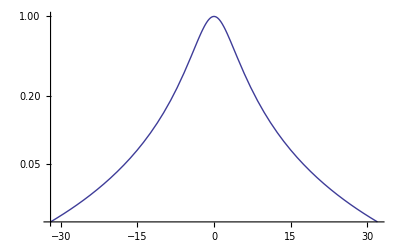

```mathematica
LogPlot[{(4g/Sqrt[16 g^2+Δ^2])^2} /. {g->1},{Δ,-32,32},PlotRange->Full]
```

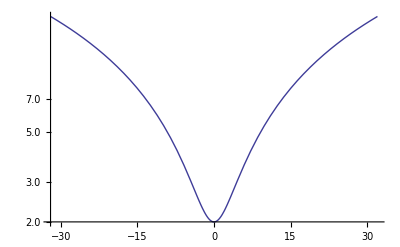

```mathematica
LogPlot[{1/2*Sqrt[16 g^2+Δ^2]} /. {g->1},{Δ,-32,32},PlotRange->Full]
```

```mathematica
Export[NotebookDirectory[]<>"swap_amplitude.csv",Map[Block[{Δ=#},{#,(4g/Sqrt[16 g^2+Δ^2])^2} /. {g->1}]&,Range[-32,32,0.01]] ]
```

E:\cygwin\home\adewes\thesis\material\mathematica\swap_amplitude.csv

```mathematica
Export[NotebookDirectory[]<>"swap_frequency.csv",Map[Block[{Δ=#},{#,1/2*Sqrt[16 g^2+Δ^2]} /. {g->1}]&,Range[-32,32,0.01]] ]
```

E:\cygwin\home\adewes\thesis\material\mathematica\swap_frequency.csv

```mathematica
Solve [(4g/Sqrt[16 g^2+Δ^2])^2 == 0.01,{Δ}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Δ→-39.7995 g},{Δ→39.7995 g}}